## Comparing points

```mathematica
SetDirectory[NotebookDirectory[]];
dataStd=ImportString[Import["SRM1976_full.txt"],"Table"][[All,1;;2]];
data=ImportString[Import["theta.txt"],"Table"][[39;;All]][[All,1;;2]];
certifiedRelativeIntensity=Import["certefied.xlsx"][[1]];
```

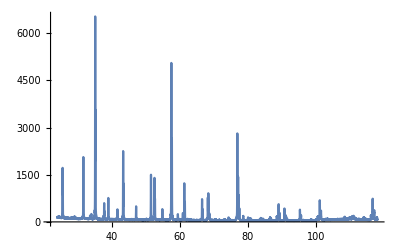

```mathematica
ListLinePlot[dataStd,PlotRange->Full]
```

```mathematica
labels=Text[#[[1]],{#[[2]],#[[3]]*65}+{0,300}]&/@certifiedRelativeIntensity
```

{Text[012,{25.575,1884.05}],Text[104,{35.147,6800.}],Text[113,{43.351,2775.85}],Text[024,{52.548,1692.95}],Text[116,{57.495,6067.45}],Text[300,{68.207,1137.2}],Text[119,{77.229,5081.4}],Text[0.2.10,{88.989,1202.2}],Text[226,{95.242,859.65}],Text[2.1.10,{101.066,1418.65}],Text[324,{116.091,2059.55}],Text[1.3.10,{127.669,1325.7}],Text[146,{136.063,1180.75}],Text[4.0.10,{145.152,1040.35}]}

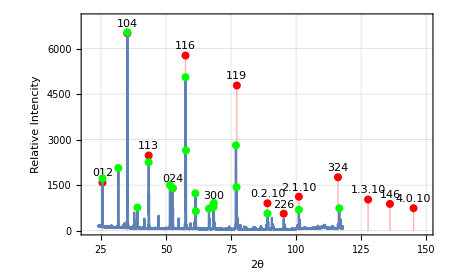

```mathematica
referencePlot=Show[
ListPlot[Transpose[{certifiedRelativeIntensity[[All,2]],certifiedRelativeIntensity[[All,3]]*65}],PlotTheme->"Detailed",FrameLabel->{"2θ","Relative Intencity"},Filling->Axis,PlotStyle->Red,PlotRange->{{20,150},{0,7000}}],
Graphics[labels,Medium],
ListLinePlot[dataStd,PlotRange->All],
ListPlot[Part[dataStd,FindPeaks[dataStd[[All,2]],4,10,200][[All,1]]],PlotStyle->Green]]
```

## Selecting points

```mathematica
peaks=FindPeaks[dataStd[[All,2]],2.3,10,200][[All,1]];
foundPeaksAngle=Part[dataStd,peaks][[All,1]];
diffTable=Abs[Table[foundPeaksAngle,Length[certifiedRelativeIntensity[[All,2]]]]-Transpose[Table[certifiedRelativeIntensity[[All,2]],Length[foundPeaksAngle]]]];
selectionTable=HeavisideTheta[0.5-diffTable];
MatrixForm[selectionTable]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Selecting approximation areas and peaks amount

General::munfl: Exp[-1110.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.178] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-854.913] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

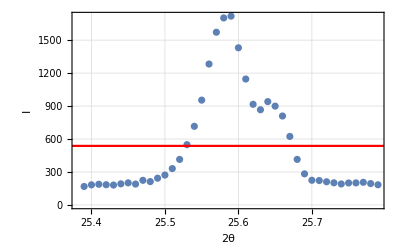
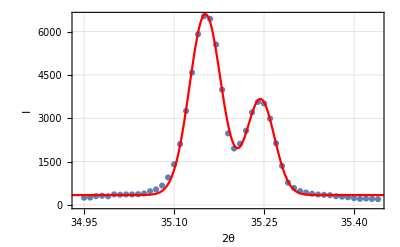
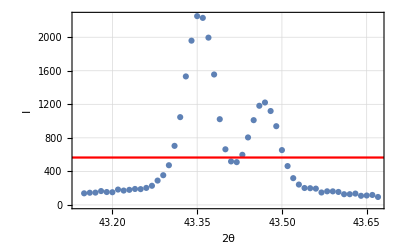
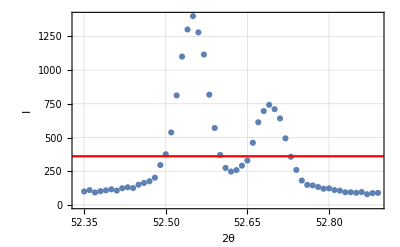
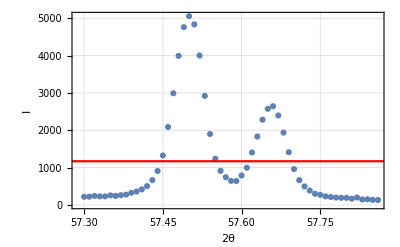
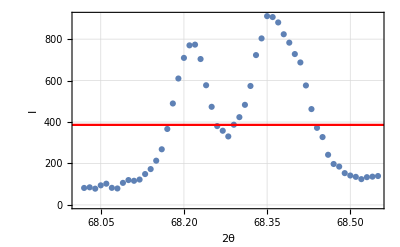
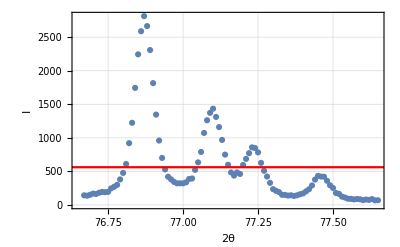
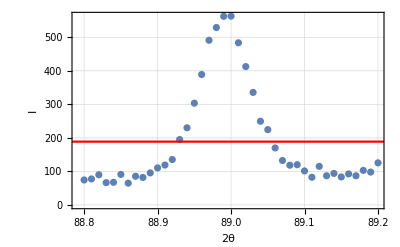

```mathematica
indexes=Transpose[FirstPosition[#,1,{0}]&/@selectionTable][[1]];
indexesLast=indexes+((Total/@selectionTable-1)/.-1->0);
mapIndexes=DeleteCases[Transpose[{indexes,indexesLast}],{0,0}];
ranges={foundPeaksAngle[[mapIndexes[[#,1]]]],foundPeaksAngle[[mapIndexes[[#,2]]]]}&/@Table[i,{i,Length[mapIndexes]}];
rangesIndexes=Transpose[{Transpose[(Position[dataStd[[All,1]],#]&/@ ranges[[All,1]])[[All,1]]][[1]]-20,Transpose[(Position[dataStd[[All,1]],#]&/@ ranges[[All,2]])[[All,1]]][[1]]+20}];
plotsValues=(dataStd[[#[[1]];;#[[2]]]]&/@rangesIndexes);
g[x_]:=a1*Exp[-(x-b1)^2/(2 c1^2)]+a2*Exp[-(x-b2)^2/(2 c2^2)]+h0;
l[x_]:=1/π(G1/((x-x01)^2+G1^2))+1/π(G2/((x-x02)^2+G2^2));
fitD=Quiet@NonlinearModelFit[plotsValues[[#]],g[x],{a1,b1,c1,a2,b2,c2,h0},x]&/@Table[i,{i,Length[plotsValues]}];
plots=Show[
ListPlot[plotsValues[[#]],PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"2θ","I"}],
Plot[Normal[fitD[[#]]],{x,ranges[[#,1]]-1,ranges[[#,2]]+1},PlotRange->Full,PlotStyle->Red]
]&/@Table[i,{i,Length[plotsValues]}]
```

# Approximation failed

```mathematica
(*Export["reference.svg",referencePlot,ImageSize->Full]*)
```

```mathematica
(*Export["peaksPlot.svg",peaksPlot,ImageSize->Full]*)
```

## Approximation test

```mathematica
foundPeaks
```

{{25.59,1718.5},{31.67,2062.},{35.15,6533.5},{35.24,3565.5},{43.35,2251.5},{51.53,1499.5},{52.55,1400.},{57.5,5055.},{57.66,2644.},{76.87,2813.5}}

Data we want to approximate

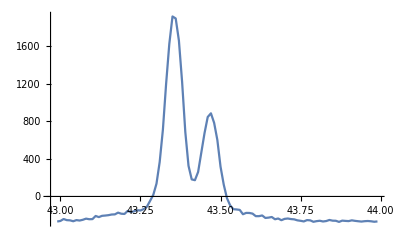

```mathematica
d1=dataStd[[1900;;2000]]-Table[{0,Mean[dataStd[[1900;;2000,2]]]},Length[dataStd[[1900;;2000]]]];
ListLinePlot[d1,PlotRange->All]
```

Now a bit of magic...

```mathematica
fitD1=FindFit[d1,g[x],{a1,b1,c1,a2,b2,c2},x]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{a1→1.,b1→1.,c1→1.,a2→1.,b2→1.,c2→1.}

Let' s look at the result of our work!

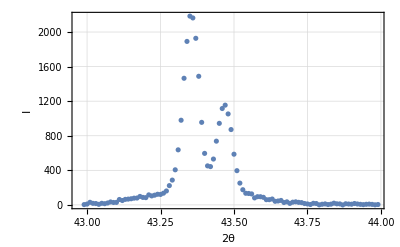

```mathematica
Show[
ListPlot[d1,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"2θ","I"}],
Plot[Normal[fitD1],{x,43,44},PlotRange->Full,PlotStyle->Red]
]
```

Our parameters and their uncertainties

```mathematica
fitD1["ParameterErrors"]
```

General::munfl: Exp[-881.58] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-882.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-882.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,0.,0.,0.,0.,0.,50.3873}

```mathematica
g[x]
```

a1 ⅇ^(-(-b1+x)^2/(2 c1^2))

```mathematica
FindPeaks[dataStd[[All,2]],2.3,20,300]
```

{{160,1718.5},{768,2062.},{1116,6533.5},{1125,3565.5},{1380,596.5},{1501,761.},{1936,2251.5},{1948,1221.5},{2317,494.5},{2754,1499.5},{2856,1400.},{2870,742.},{3351,5055.},{3367,2644.},{3731,1227.5},{3748,639.},{4253,723.5},{4423,773.5},{4436,911.},{5288,2813.5},{5311,1434.},{5324,858.},{6501,563.},{7707,687.}}

-27.4977+11.8176 x

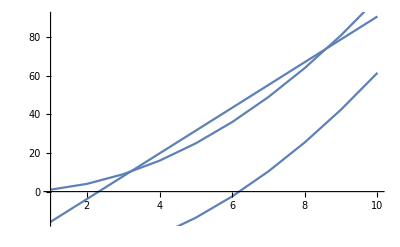

```mathematica
a=LinearModelFit[Range[10]^2,x,x,Weights->(Sqrt[#]&)]["BestFit"]
Show[Plot[a,{x,1,10}],ListLinePlot[Range[10]^2],ListLinePlot[Range[10]^2-Mean[Range[10]^2]]]
```

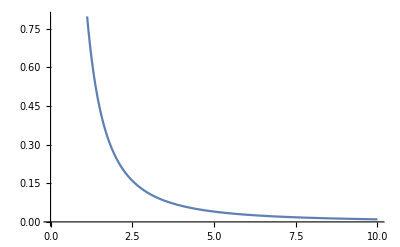

```mathematica
Plot[1/x^2,{x,0,10}]
```

```mathematica
Export["referencePlot.png",referencePlot,ImageSize->700]
```

referencePlot.png